```mathematica
xs = RandomReal[NormalDistribution[], 500];
```

```mathematica
ys = xs^2 - 1 + RandomReal[NormalDistribution[0, 0.3], 500];
```

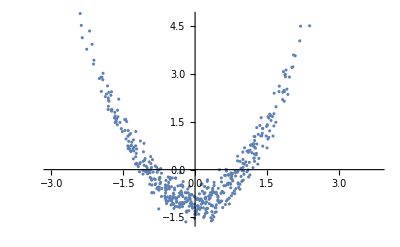

```mathematica
ListPlot[Transpose[{xs, ys}]]
```

```mathematica
tdata = {#1}->{#2} &@@@Transpose[{xs, ys}];
```

```mathematica
net = NetTrain[NetInitialize[
NetChain[{LinearLayer[2], Tanh, LinearLayer[1]}, "Input"-> 1], 
Method-> {"Xavier", "FactorType"-> "Mean", "Distribution"-> "Normal"}
],
tdata,
LossFunction->MeanSquaredLossLayer[],
MaxTrainingRounds->2000,
Method-> "ADAM"];
```

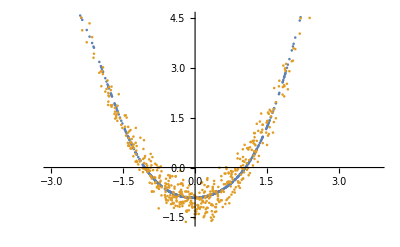

```mathematica
ListPlot[{
{#, net[{#}][[1]]}&/@ Sort@xs,
Transpose[{xs, ys}]
}]
```

```mathematica
{{L1w11} ,{L1w21}} = NetExtract[net, {1, "Weights"}];
{L1b1, L1b2}= NetExtract[net, {1, "Biases"}];
{{L2w11, L2w12}} = NetExtract[net, {3, "Weights"}];
{L2b1} = NetExtract[net, {3, "Biases"}];
```

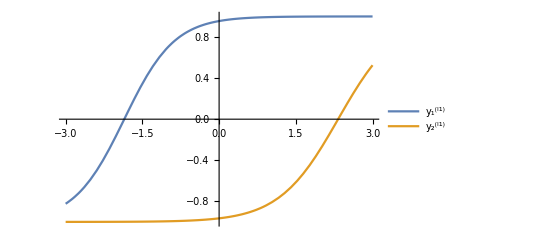

```mathematica
Plot[{Tanh[L1w11 x + L1b1], Tanh[L1w21 x + L1b2]}, {x, -3, 3},
PlotLegends->{"y_1^(l1)", "y_2^(l1)"}]
```

```mathematica
L2w11
```

-3.9174

```mathematica
L2w12
```

6.54133

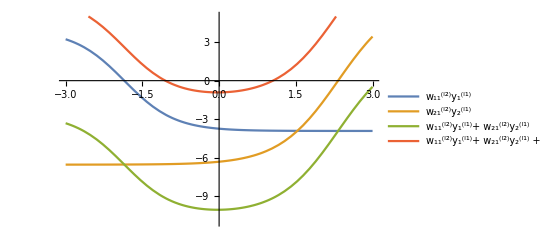

```mathematica
Plot[{L2w11 Tanh[L1w11 x + L1b1],
L2w12 Tanh[L1w21 x + L1b2],
L2w11 Tanh[L1w11 x + L1b1]+ L2w12 Tanh[L1w21 x + L1b2],
L2w11 Tanh[L1w11 x + L1b1]+ L2w12 Tanh[L1w21 x + L1b2] + L2b1
}, {x, -3, 3},
PlotRange->{{-3, 3},{-11, 5}},
PlotLegends->{
"w_11^(l2)y_1^(l1)",
"w_21^(l2)y_2^(l1)",
"w_11^(l2)y_1^(l1)+ w_21^(l2)y_2^(l1)",
"w_11^(l2)y_1^(l1)+ w_21^(l2)y_2^(l1) + b_1^(l2) = y_1^(l2)"}]
```